```mathematica
(* Run this set of commands to check if the Lsep, Rmin, Smin values are correct *)
(* R. Sheehan November 2018 *)
```

## Length of all arrayed waveguides given Rmin, Smin and θmin

```mathematica
T1=-0.268184; (* Angle that first array waveguide makes with horizontal *)
dT = Abs[0.268184 - 0.256524]; (* angle separation between array waveguides on input/output aperture *)
Lf=857.62; (* length of slab region *)
Sn=20; (* min. length of array straight section *)
Rn=2000;(* smallest array bend radius *)
dL=138.63; (* Array optical path-length difference *)
nn=47; (* Number of arrayed Waveguides *)
```

```mathematica
Sep[Rn_,Ta_,Ti_,Lf_,Sn_]:=2(Rn Sin[Ti+Ta]+(Lf+Sn)Cos[Ti+Ta]); (* separation between slab regions *)
```

```mathematica
Ltj[Sn_,Rn_,Ti_,Ta_,dL_,j_]:=Sn+Rn (Ti+Ta)+(j-1)dL/2;(* Known length of jth arm of arrayed waveguide *)
```

```mathematica
(* Test to see if the numerical and analytical formulae give the same answer for slab separation *)
data=FindMaximum[Sep[Rn,x,T1,Lf,Sn],{x,(70π)/180}];(* Find angle Ta which maximises slab separation *)
Ta=ArcTan[Rn/(Lf+Sn)]-T1; (* Exact value of angle Ta which maximises slab separation *)
Ls=Sep[Rn,Ta,T1,Lf,Sn]; (* Computed slab separation *)

Print["Numerical Ta-deg = ",(180data⟦2,-1,-1⟧)/π,", Ta-rad = ",data⟦2,-1,-1⟧,", Analytical θ^a = θ_n^max - θ_i^s = ",Ta," rad"]
Print["Numerical 1/2Ls = ",data⟦1⟧/2," um, Analytical 1/2Ls = ",Ls/2," um"]
Print["Min Length: Sn + Rn (T1 + Ta) = ",Sn+Rn (T1+Ta)]
```

Numerical Ta-deg = 81.6735, Ta-rad = 1.42547, Analytical θ^a = θ_n^max - θ_i^s = 1.42547 rad

Numerical 1/2Ls = 2184.08 um, Analytical 1/2Ls = 2184.08 um

Min Length: Sn + Rn (T1 + Ta) = 2334.57

```mathematica
alllengths = Table[{Ta+T1+(j-1)dT,Ltj[Sn,Rn,T1,Ta,dL,j]},{j,1,nn,1}]; (* Compute all known lengths of the AWG arms *)
```

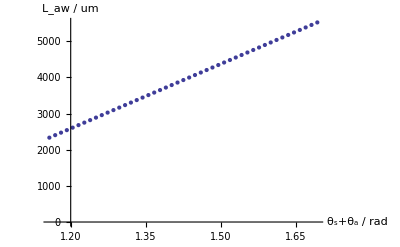

```mathematica
ListPlot[alllengths,AxesLabel->{"θ_s+θ_a / rad","L_aw / um"}]
```

```mathematica
(* Test to see if one of the constraints is satisfied *)
j=1;
While[j≤ nn,
LHS = 2(Lf+alllengths⟦j,2⟧)Cos[Ta+T1+(j-1)dT];
If[LHS>Ls,Print["j = ",j,", LHS = ",LHS,", Ls = ",Ls,", LHS > Ls ⇒ Rj < 0"];Break[];];
j++
]
```

```mathematica
allradii=Table[{Ta+T1+(j-1)dT,(Ls/2-(Lf+alllengths⟦j,2⟧)Cos[Ta+T1+(j-1)dT])/(Sin[Ta+T1+(j-1)dT]-(Ta+T1+(j-1)dT)Cos[Ta+T1+(j-1)dT])},{j,1,nn,1}];
```

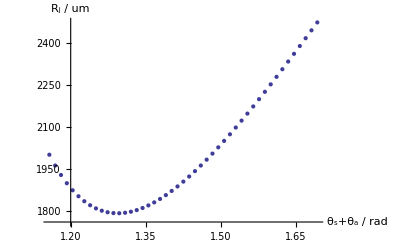

```mathematica
ListPlot[allradii,AxesLabel->{"θ_s+θ_a / rad","R_j / um"}]
```

```mathematica
allss=Table[{Ta+T1+(j-1)dT,alllengths⟦j,2⟧-allradii⟦j,2⟧(Ta+T1+(j-1)dT)},{j,1,nn,1}];
```

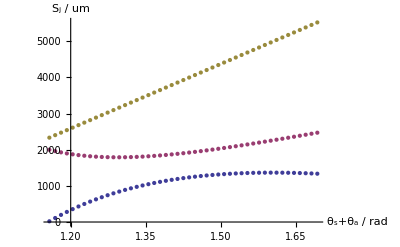

```mathematica
ListPlot[{allss,allradii,alllengths},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}]
```

```mathematica
alltotalL=Table[{Ta+T1+(j-1)dT,(allss⟦j,2⟧+allradii⟦j,2⟧(Ta+T1+(j-1)dT))},{j,1,nn,1}];
```

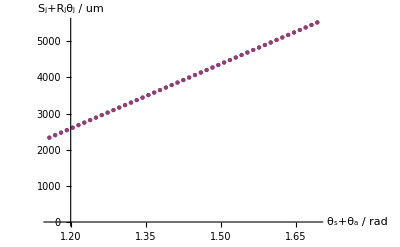

```mathematica
ListPlot[{alltotalL,alllengths},AxesLabel->{"θ_s+θ_a / rad","S_j+R_jθ_j / um"}]
```

```mathematica
alldiffl=Table[{Ta+T1+(j-1)dT,alllengths⟦j,2⟧-(allss⟦j,2⟧+allradii⟦j,2⟧(Ta+T1+(j-1)dT))},{j,1,nn,1}];
```

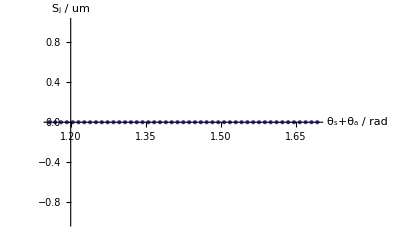

```mathematica
ListPlot[alldiffl,AxesLabel->{"θ_s+θ_a / rad","S_j / um"}]
```

```mathematica
allconstraints=Table[{Ta+T1+(j-1)dT,((Lf+allss⟦j,2⟧)Cos[Ta+T1+(j-1)dT]+allradii⟦j,2⟧Sin[Ta+T1+(j-1)dT])-Ls/2},{j,1,nn,1}];
```

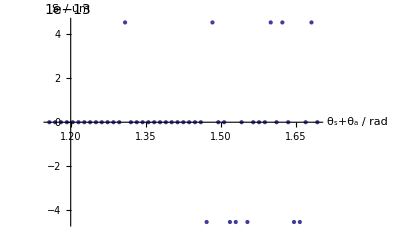

```mathematica
ListPlot[allconstraints,AxesLabel->{"θ_s+θ_a / rad","S_j / um"}]
```